```mathematica
evos =Select[ , #[[-1]] == 100&];
```

```mathematica
evos4 = Select[, #[[-1]] == 100&];
```

### Contour Plot for Random Binary Walk

```mathematica
walks = ;
```

```mathematica
ArrayPlot/@ Map[CenterArray[Table[1, 2#],60]&, walks, {2}][[;;3]]
```

{-Graphics-,-Graphics-,-Graphics-}

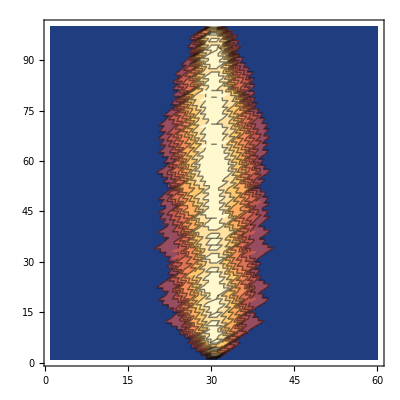

```mathematica
ListContourPlot[Reverse@Map[Total[#]&,Transpose[Map[CenterArray[Table[1, 2#],60]&, walks, {2}],{3,1,2}],{2}]]
```

Evolved for comparison:

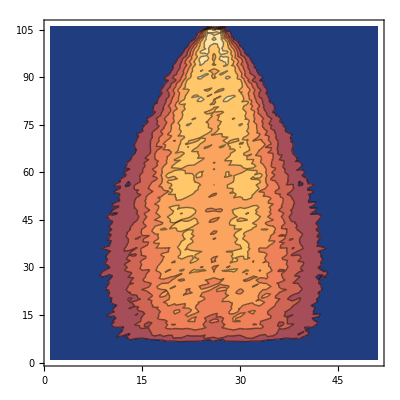

```mathematica
With[{re=Select[,Last[#]==100&][[All,1]]},ListContourPlot[Reverse@Map[Total[#]&,Transpose[CellularAutomaton[#,{{1},0},{105,{-25,25}}]&/@re,{3,1,2}],{2}]]]
```

### Image Analysis

#### Morphological graph of evolved from random

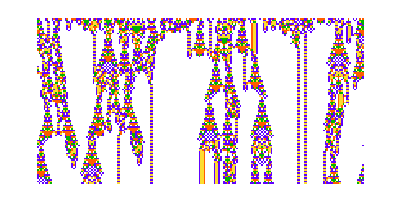

```mathematica
SeedRandom[111154];ArrayPlot[CellularAutomaton[RandomChoice[evos][[1]], RandomInteger[2, 200], 100],ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99], 4->RGBColor[0, 0.7000000000000001, 0]}]
```

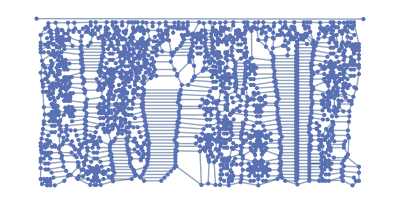

```mathematica
MorphologicalGraph[Binarize[]]
```

Rule 30 for comparison:

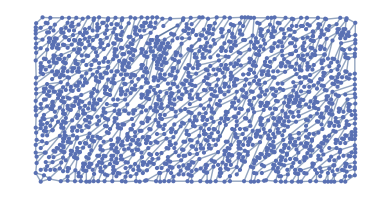

```mathematica
MorphologicalGraph[ArrayPlot[CellularAutomaton[30, RandomInteger[1, 200], 100]]]
```

#### Starting from seed morphological graph (k = 5)

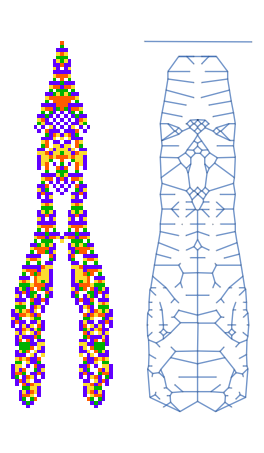
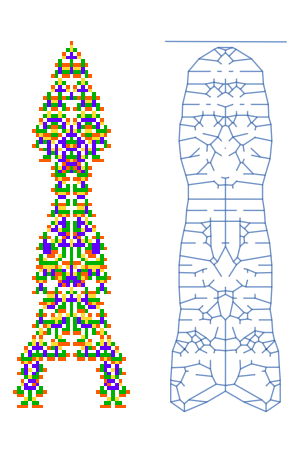

```mathematica
SeedRandom[111154];With[{ap = ArrayPlot[CellularAutomaton[#, {{1}, 0}, 100],ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99], 4->RGBColor[0, 0.7000000000000001, 0]}]},GraphicsRow[{ap,  MorphologicalGraph[Binarize[ap]]}]]&/@ RandomSample[evos[[All,1 ]], 2]
```

#### All skeleton transforms from seed (k = 5)

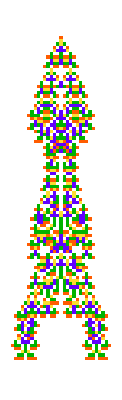
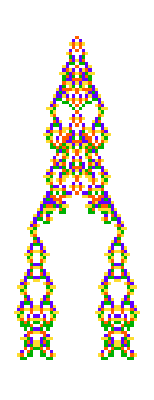

```mathematica
With[{ap =ArrayPlot[CellularAutomaton[#, {{1}, 0}, 100],ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99], 4->RGBColor[0, 0.7000000000000001, 0]}]}, GraphicsRow[{ap, ColorNegate[SkeletonTransform[Binarize[ap]]]}]]&/@ RandomSample[evos[[All, 1]], 2]
```

```mathematica
SeedRandom[333222];ParallelMap[ColorNegate[SkeletonTransform[ArrayPlot[CellularAutomaton[#, {{1}, 0}, 105]]]]&, Select[evos, #[[2]] == 100&][[All, 1]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Blended

```mathematica
Blend[]
```

-Graphics-

#### TODO: Get causal graph working

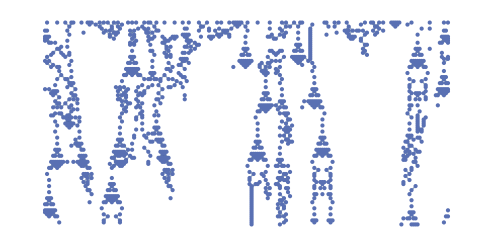

```mathematica
SeedRandom[111154];
NearestNeighborGraph[Position[Transpose[
Reverse[CellularAutomaton[RandomChoice[evos][[1]], RandomInteger[2, 200], 100]]],1], {All,2Sqrt[2]}]
```

### Evolved Patterns All Have a Similar Hausdorff Dimension

```mathematica
GraphicsGrid[ArrayPlot[#, Mesh->True, MeshStyle->Opacity[.1]]&/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, #, UpTo[Ceiling[# / divs]]&/@ Dimensions[#]]]]/@ Table[2^n, {n,2, 7}])&/@ (CellularAutomaton[#, {{1}, 0}, 105]&/@ evos[[;;4, 1]])]
```

-Graphics-

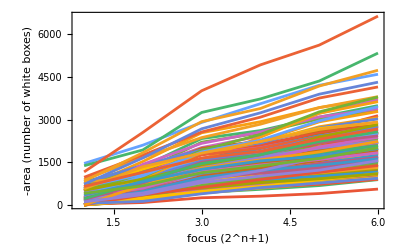

```mathematica
ListLinePlot[Count[#, 0, {2}]&/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, #, UpTo[Ceiling[# / divs]]&/@ Dimensions[#]]]]/@ Table[2^n, {n,2, 7}])&/@ (CellularAutomaton[#, {{1}, 0}, 105]&/@ evos[[All, 1]]), PlotRange->All, PlotHighlighting->None, Frame->True, FrameLabel->{"focus (2^n+1)", "-area (number of white boxes)"}]
```

#### How does this algorithm work?

```mathematica
GraphicsRow[MapThread[ArrayPlot[#1,Mesh->#2, MeshStyle->Opacity[Length[#2[[1]]]^-.6], ColorRules->{1->GrayLevel[.5]}]&, {(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, #, UpTo[Ceiling[# / divs]]&/@ Dimensions[#]]]]/@ Table[2^n, {n,2, 7}])&@ (CellularAutomaton[#, {{1}, 0}, 105]&@ evos[[1, 1]]), Function[divs, Append[Table[i, {i, 0, # - 2,Ceiling[# / divs]}], #]&/@ Dimensions[CellularAutomaton[evos[[1, 1]], {{1}, 0}, 105]]]/@Table[2^n, {n,2, 7}]}]]
```

-Graphics-

All white for comparison

```mathematica
GraphicsRow[MapThread[ArrayPlot[#1,Mesh->#2, MeshStyle->Opacity[Length[#2[[1]]]^-.6], ColorRules->{1->GrayLevel[.5]}]&, {(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, #, UpTo[Ceiling[# / divs]]&/@ Dimensions[#]]]]/@ Table[2^n, {n,2, 7}])&@ (ConstantArray[0, {105, 30}]), Function[divs, Append[Table[i, {i, 0, # - 2,Ceiling[# / divs]}], #]&/@ Dimensions[CellularAutomaton[evos[[1, 1]], {{1}, 0}, 105]]]/@Table[2^n, {n,2, 7}]}]]
```

-Graphics-

### Hausdorff dimension of Proteins is Qualitatively Similar to Evolved CAs

```mathematica
SeedRandom[333222];ps = ParallelSelect[RandomSample[EntityList["Protein"],1000], #[EntityProperty["Protein","WireframeDiagram"]]=!=Missing["NotAvailable"]&];
```

```mathematica
GraphicsGrid[ArrayPlot[#, ColorRules->Automatic]&/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, #, UpTo[Ceiling[# / divs]]&/@ Dimensions[#]]]]/@ Table[2^n, {n,3, 8}])&/@ (ImageData[Binarize[#[EntityProperty["Protein","WireframeDiagram"]]]]&/@ ps[[;;4]])]
```

-Graphics-

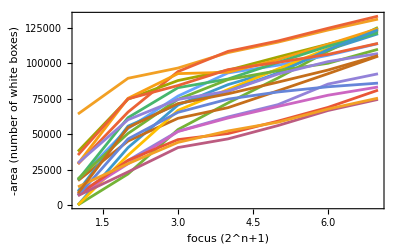

```mathematica
ListLinePlot[Count[#, 0, {2}]&/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, #, UpTo[Ceiling[# / divs]]&/@ Dimensions[#]]]]/@ Table[2^n, {n,2, 8}])&/@ (ImageData[Binarize[#[EntityProperty["Protein","WireframeDiagram"]]]]&/@ ps), PlotRange->{{1, 7}, Automatic},PlotHighlighting->None, Frame->True, FrameLabel->{"focus (2^n+1)", "-area (number of white boxes)"}]
```

### Contour Plot of Proteins

```mathematica
ListContourPlot[Reverse@Map[Total[#]&,Transpose[idata,{3,1,2}],{2}]]
```

-Graphics-

```mathematica
Blend[[[All, -1]]]
```

-Graphics-

#### TODO: Canonicalize for a better result

Fix this

```mathematica
ClearAll[normalizeShape];normalizeShape[array_]:=Module[{(*coords,com,centered,mat,v,aligned,min,shifted,dims,mask*)},coords=Position[array,1];
com=Mean[coords];
(*subtract com from each coordinate*)centered=(#-com&)/@coords;
mat=N[centered];(*now an n×2 numeric matrix*)(*PCA alignment via SVD*){_,_,v}=SingularValueDecomposition[mat];
aligned=mat.v;(*still n×2*)(*shift into positive quadrant*)min=Floor[Min/@Transpose[aligned]];
shifted=Round[aligned-min]+1;(*list of integer {i,j} pairs*)(*rasterize back into a 2D binary mask*)dims=Max/@shifted;
mask=ConstantArray[0,dims];
Do[mask[[Sequence@@shifted[[i]]]]=1,{i,Length[shifted]}];
mask
];
```